```mathematica
SetDirectory[NotebookDirectory[]];
```

```mathematica
aRange={{-10,25},Full};
g[x_]:=PDF[NormalDistribution[5,5],x]
gActual=Rotate[Plot[g[x],{x,-10,25},Frame->{True,True,False,False},FrameTicks->{False,False,False,False},FrameLabel->{"θ",Rotate["p(θ|data)",Pi]},PlotStyle->Orange,PlotRange->aRange,Axes->None],Pi/2];
fProposal[θ_,σ_]:=RandomVariate[NormalDistribution[θ,σ],{1}][[1]]
fSingleStepMetropolis[θ_,σ_,aF_]:=Module[{aProposedTheta=fProposal[θ,σ],aRand=RandomReal[]},If[aF[aProposedTheta]>aF[θ],aProposedTheta,If[aRand<aF[aProposedTheta]/aF[θ],aProposedTheta,θ]]]
fStepMetropolis[nSteps_,aStart_,σ_,aF_]:=NestList[fSingleStepMetropolis[#,σ,aF]&,aStart,nSteps]
fGetCorrelation[lSeries__,aMaxLag_Integer]:=ParallelTable[{lag,CorrelationFunction[lSeries,lag]},{lag,0,aMaxLag}]
fGetMaxT[lCor__]:=FirstPosition[MovingMap[(#[[1]]+#[[2]])&,lCor[[All,2]],2],_?Negative][[1]]
fGetEffectiveSamplesOverTime[lSeries__,aMaxLag_]:=Module[{aVar=Variance@lSeries,lCorr=fGetCorrelation[lSeries,aMaxLag][[2;;]],aMaxT},aMaxT=fGetMaxT[lCorr];Table[If[n<aMaxT,{n,n/(1+2 Total@lCorr[[All,2]][[1;;n]])},{n,n/(1+2 Total[lCorr[[All,2]][[1;;aMaxT]]])}],{n,1,aMaxLag}]]
```

```mathematica
n=1000;
```

```mathematica
dataMetropolisSmall=fStepMetropolis[n,18,0.1,g];
```

```mathematica
dataMetropolisJustRight=fStepMetropolis[n,18,8,g];
```

```mathematica
dataMetropolisLarge=fStepMetropolis[n,18,200,g];
```

```mathematica
g2a=Histogram[dataMetropolisSmall,{10.83/10},PlotRange->Reverse@aRange,Axes->None,BarOrigin->Right,Frame->{True,False,False,False},FrameLabel->{"frequency","θ"},BaseStyle->{FontSize->Medium},ChartStyle->Blue];
g1a=ListLinePlot[dataMetropolisSmall,Axes->None,PlotRange->Reverse@aRange,PlotStyle->Blue,Frame->{True,True,False,False},FrameLabel->{"step #","θ"},BaseStyle->{FontSize->Medium},FrameTicks->{True,True}];
g3a=Rotate[SmoothHistogram[dataMetropolisSmall,1,Axes->None,PlotStyle->{Dashed,Blue},PlotRange->aRange,Frame->{True,True,False,False},FrameTicks->{False,False,None,None},FrameLabel->{"θ",Rotate["p(θ|data)",Pi]}],Pi/2];
g2b=Histogram[dataMetropolisJustRight,{1},Axes->None,PlotRange->Reverse@aRange,BarOrigin->Right,Frame->{True,False,False,False},FrameLabel->{"frequency","θ"},BaseStyle->{FontSize->Medium},ChartStyle->Blue];
g1b=ListLinePlot[dataMetropolisJustRight,Axes->None,PlotRange->Reverse@aRange,PlotStyle->Blue,Frame->{True,True,False,False},FrameLabel->{"step #","θ"},BaseStyle->{FontSize->Medium},FrameTicks->{True,True}];
g3b=Rotate[SmoothHistogram[dataMetropolisJustRight,1,Axes->None,PlotStyle->{Dashed,Blue},PlotRange->aRange,Frame->{True,True,False,False},FrameTicks->{False,False,None,None},FrameLabel->{"θ",Rotate["p(θ|data)",Pi]}],Pi/2];
g2c=Histogram[dataMetropolisLarge,{10.83/10},Axes->None,PlotRange->Reverse@aRange,BarOrigin->Right,Frame->{True,False,False,False},FrameLabel->{"frequency","θ"},Axes->None,BaseStyle->{FontSize->Medium},ChartStyle->Blue];
g1c=ListLinePlot[dataMetropolisLarge,PlotRange->Reverse@aRange,PlotStyle->Blue,Frame->{True,True,False,False},FrameLabel->{"step #","θ"},BaseStyle->{FontSize->Medium},Axes->None,FrameTicks->{True,True}];
g3c=Rotate[SmoothHistogram[dataMetropolisLarge,1,Axes->None,PlotStyle->{Dashed,Blue},PlotRange->aRange,Frame->{True,True,False,False},FrameTicks->{False,False,None,None},FrameLabel->{"θ",Rotate["p(θ|data)",Pi]}],Pi/2];
gFinal=Show[GraphicsGrid[{{g1a,g2a,g3a,gActual},{g1b,g2b,g3b,gActual},{g1c,g2c,g3c,gActual}}],ImageSize->1200]
```

-Graphics-

```mathematica
Export["metropolisHastings_rateOfConvergence.pdf",gFinal]
```

metropolisHastings_rateOfConvergence.pdf

## Based on the series above now calculate interesting things

```mathematica
corSmall=fGetCorrelation[dataMetropolisSmall,20];
corLarge=fGetCorrelation[dataMetropolisLarge,20];
corJustRight=fGetCorrelation[dataMetropolisJustRight,20];
eSSSmall=fGetEffectiveSamplesOverTime[dataMetropolisSmall,1000];
eSSLarge=fGetEffectiveSamplesOverTime[dataMetropolisLarge,1000];
lKSLarge=ParallelTable[{n,Quiet[KolmogorovSmirnovTest[dataMetropolisLarge[[1;;n]],NormalDistribution[5,5],"TestData"][[1]]]},{n,1,1000,1}];
lKSSmall=ParallelTable[{n,Quiet[KolmogorovSmirnovTest[dataMetropolisSmall[[1;;n]],NormalDistribution[5,5],"TestData"][[1]]]},{n,1,1000,1}];
```

```mathematica
eSSJustRight=fGetEffectiveSamplesOverTime[dataMetropolisJustRight,1000];
```

```mathematica
lKSJustRight=ParallelTable[{n,Quiet[KolmogorovSmirnovTest[dataMetropolisJustRight[[1;;n]],NormalDistribution[5,5],"TestData"][[1]]]},{n,1,1000,10}];
```

```mathematica
lIndependentSamples = RandomVariate[NormalDistribution[5,5],{1002}];
lKSIndependent=ParallelTable[{n,Quiet@KolmogorovSmirnovTest[lIndependentSamples[[1;;n]],NormalDistribution[5,5],"TestData"][[1]]},{n,1,1000}];
```

```mathematica
corIndependent=fGetCorrelation[lIndependentSamples,20];
eSSIndependent=fGetEffectiveSamplesOverTime[lIndependentSamples,1000];
```

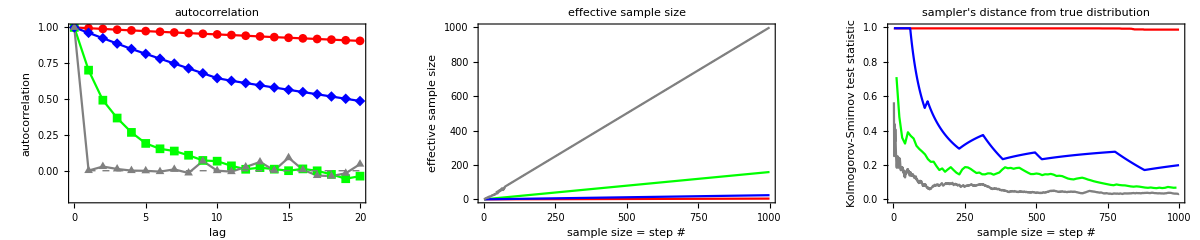

```mathematica
gFinal1=Show[GraphicsRow[{Show[ListPlot[{corSmall,corJustRight,corLarge,corIndependent},FrameLabel->{"lag","autocorrelation"},PlotLabel->"autocorrelation",PlotRange->{Automatic,{-0.2,1}},Axes->None,Joined->True,PlotMarkers->Automatic,PlotStyle->{Red,Green,Blue,Gray},Frame->{True,True,False,False},BaseStyle->{FontSize->12}],Plot[0,{x,1,1000},PlotStyle->{Thick,Gray,Dashed}]],Show[ListLinePlot[{eSSSmall,eSSJustRight,eSSLarge,eSSIndependent},PlotLabel->"effective sample size",Frame->{True,True,False,False},BaseStyle->{FontSize->12},FrameLabel->{"sample size = step #","effective sample size"},PlotRange->{Automatic,{0,1000}},PlotStyle->{Red,Green,Blue,Gray}],Plot[x,{x,0,1000},PlotStyle->{Thick,Gray,Dashed}]],ListLinePlot[{lKSSmall,lKSJustRight,lKSLarge,lKSIndependent},PlotLabel->"sampler's distance from true distribution",Frame->{True,True,False,False},BaseStyle->{FontSize->12},FrameLabel->{"sample size = step #","Kolmogorov-Smirnov test statistic"},PlotRange->{Automatic,{0,1}},PlotStyle->{Red,Green,Blue,Gray}]}],ImageSize->1200]
```

```mathematica
Export["metropolisHastings_rateOfConvergence1.pdf",gFinal1]
```

metropolisHastings_rateOfConvergence1.pdf